# The New Seeker

Brian Beckman
17 Aug 2019

## Introduction

### DEFINITIONS

Episode, Rollouts | parallelizable bunch of rollouts
Rollout, Trials, Trajectory | parallelizable bunch of trials
Trial | non–parallelizable sequence of judgments
Judgment | choice between alternative A and alternative B
Guess | pair of d–vectors, labeled A and B

## Sampling

## Uniform in d-Ball—2 [ n, d ]

```mathematica
ClearAll[uniformInBall2];
uniformInBall2[n_:50000,d_:2]:=
Drop[#,2]&/@
Normalize/@
RandomVariate[
NormalDistribution[],{n,d+2}];
```

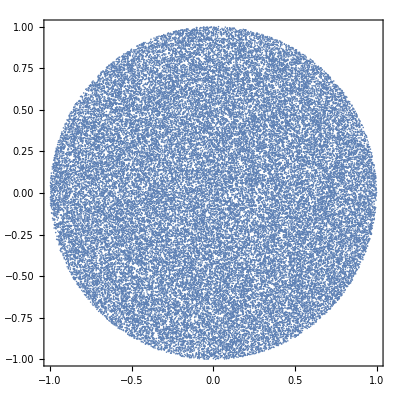

```mathematica
ListPlot[uniformInBall2[],AspectRatio->Automatic,Frame->True]
```

## Seeking

## Bisecting for the Decay

For each dim, tol, maxIter, find, via bisection, the smallest decay Δ that converges 100% rollouts in an episode, i.e., in the smallest number of a/b judgments. 

A bad search can die or it can wander. A search dies when its center yp is 10 × maxIter × σ away from tar; (TODO: check the following assertion!) the chances that new a/b guesses will converge in the remaining judgments are small. A search wanders when it fails to converge within tol after maxIter trials; it runs out of gas looking. To find out whether a search wanders, we must follow it to the bitter end; that’s expensive, explaining the death test. 

Here is a version of nexter that throws when it dies or wins, to avoid wasting computation, or wanders, so we can handle this case the same way we handle the other two cases. It decays σ rather than covariance, σ^2. It’s a continuing ambiguity in this research whether to decay σ or variance = σ^2; It may not matter, it might matter; I don’t know yet.

```mathematica
ClearAll[getTarget];
getTarget[d_:4]:=uniformInBall2[1,d]⟦1⟧;
```

nexter002 should be called from Fold wrapped in three nested Catches, one each for “Found,” “Dead,” and “Wandering.” Intermediate points are sown out, where a caller can reap them for visualization. Just in case Sow turns out to be expensive, we call it through a pointer, sow, in lower case, that you can set to Identity when you don’t need to reap the intermediate points.

```mathematica
(* set "sow" to "Identity" to save time when you don't need to reap. *)
sow=Sow;
ClearAll[nexter002];
nexter002[{yp_,dist_,σ_},{Δ_,tar_,tol_,maxIter_,i_}]:=
(* 8 parameters; account for all of them: *)
Module[{a,b,da,db,d},
(* (2) dist, σ used *)
If[(dist>10maxIter σ),Throw[{yp,dist,σ,tar,Δ,i},"Dead"]];
(* (4) maxIter, i used *)
If[i≥maxIter,Throw[{yp,dist,σ,tar,Δ,i},"Wandering"]]; 
(* (5) yp used *)
a=Map[RandomVariate[NormalDistribution[#,σ]]&,yp];
b=Map[RandomVariate[NormalDistribution[#,σ]]&,yp];
(* (6) tar used *)
da=EuclideanDistance[tar,a];
(* (7) tol used *)
If[da<tol,Throw[{a,da,σ,tar,Δ,i},"Found"]];
db=EuclideanDistance[tar,b];
If[da<tol,Throw[{b,db,σ,tar,Δ,i},"Found"]];
(* (8) Δ used *)
With[{νσ=Quiet[σ*Δ]},
sow@If[da<db,
{a,da,νσ},
{b,db,νσ}]]];
```

```mathematica
ClearAll[trialDict];
trialDict[{yp_,dist_,σ_,tar_,Δ_,i_},tag_]:=
<|"yp"->yp,"dist"->dist,"σ"->σ,"tar"->tar,"Δ"->Δ,"i"->i,"tag"->tag|>;
```

```mathematica
ClearAll[vizSeek2D,vizSeek2D002,dist,yp,σ,cov,i];
picker[n_]:=#⟦n⟧&;{yp,dist,σ}=picker/@Range[3];
echo=Echo;
DBALLRADIUS=1.0;
vizSeek2D002[tol_:0.1,Δ_:0.99599,maxIter_:10000,pr_:10,dim_:2]:=
(* For picking a random pair of dims for display from big-dim vectors. *)
With[{indices=Sort@RandomSample[Range[dim],2]},
With[{indexer={#⟦indices⟦1⟧⟧,#⟦indices⟦2⟧⟧}&},
With[{sampler={indexer[yp[#]],dist[#],σ[#]}&},
With[{tar=getTarget[dim],ini=ConstantArray[0,dim]},
With[{result=Reap[Catch[Catch[Catch[Fold[
nexter002,{ini,0,DBALLRADIUS},
Table[{Δ,tar,tol,maxIter,i},{i,maxIter}]],
"Found",trialDict],"Dead",trialDict],"Wandering",trialDict]
]},
With[{tag=result⟦1⟧["tag"],points=result⟦2,1⟧,smtar=indexer@tar,sampled=sampler/@result⟦2,1⟧,l=Length[result⟦2,1⟧]},
Show[Graphics[{
LightGray,Disk[],White,Disk[smtar,0.3],Black,Circle[smtar,0.3],
MapIndexed[
{Hue[(2.+#2*4/l)/6.],Circle[yp[#1],σ[#1]],Point[yp[#1]]}&,
sampled],
Text[Style[{l,tag(*,Δ,tol*),σ[Last[sampled]]},"Text",Background->White],{0,pr*0.960}]
}],AspectRatio->Automatic,Frame->True,PlotRange->1.025*pr]]]]]]];
Manipulate[
vizSeek2D002[10.^le,1.-10^-ld,Floor[10.^lm],r,dim],
Row[{Button["  DO AGAIN  ",(le++;le--)&],"    ",
Button["  RESET  ",(le=-2;ld=1.0;lm=2;r=2;dim=2)&]}],
{{le,-2,"log_10(tol)"},-5,0,0.1,Appearance->{"Open","Labeled"}},
{{ld,1.0,"-log_10(1-Δ)"},0.,5.,0.25,Appearance->{"Open","Labeled"}},
{{lm,3,"log_10(reps)"},0,7,1,Appearance->{"Open","Labeled"}},
{{r,2,"plot range"},1,30,1,Appearance->{"Open","Labeled"}},
{{dim,2},{2,5,10,20,50,100,200,500,1000,2000,5000,10000},ControlType->Setter}]
```

```mathematica
ClearAll[cume,zeroStats];
zeroStats=<|"mean"->0,"min"->Infinity,"max"->-Infinity,"var"->0,"n"->0,"stddev"->0|>;
cume[runningStats_,z_]:=
With[{
m=runningStats["mean"],
max=runningStats["max"],
min=runningStats["min"],
n=runningStats["n"],
var=runningStats["var"]},
With[{K=1./(n+1.),r=z-m},
With[{var2=((n-1)var+K n r^2)/Max[1,n]},
<|"mean"->m+K r,"n"->n+1,"min"->Min[z,min],
"max"->Max[z,max],"var"->var2,"stddev"->Sqrt[var2]|>]]];
(*FoldList[cume,zeroStats,{55,89,144}]*)
```

Here is a version that does not Sow all its points, to save memory

```mathematica
Block[{sow=Identity},
ClearAll[trial];
trial[Δ_,tar_,tol_,maxIter_]:=
Module[{tagg},
Catch[Catch[Catch[
Fold[nexter002,
{ConstantArray[0.,Length@tar],0.,1.},
Table[{Δ,tar,tol,maxIter,i},{i,maxIter}]],
"Found",trialDict],"Dead",trialDict],"Wandering",trialDict]];
trial[.99599,getTarget[2],0.01,1000]]
```

<|yp→{-0.524103,0.713092},dist→0.00879827,σ→0.0901015,tar→{-0.516574,0.708538},Δ→0.99599,i→600,tag→Found|>

```mathematica
ClearAll[printSeek2D002];
printSeek2D002[tol_:0.1,Δ_:0.99599,maxIter_:10000,pr_:10,dim_:2]:=
Block[{sow=Identity},
(* For picking a random pair of dims for display from big-dim vectors. *)
With[{indices=Sort@RandomSample[Range[dim],2]},
With[{indexer={#⟦indices⟦1⟧⟧,#⟦indices⟦2⟧⟧}&},
With[{sampler={indexer[yp[#]],dist[#],σ[#]}&},
With[{tar=getTarget[dim],ini=ConstantArray[0,dim]},
With[{result=Reap[Catch[Catch[Catch[Fold[
nexter002,{ini,0,DBALLRADIUS},
Table[{Δ,tar,tol,maxIter,i},{i,maxIter}]],
"Found",trialDict],"Dead",trialDict],"Wandering",trialDict]]},
<|"σ"->result⟦1⟧["σ"],"i"->result⟦1⟧["i"],"tag"->result⟦1⟧["tag"],"Δ"->Δ,"dim"->dim,"tol"->tol|>]]]]]];
Manipulate[
printSeek2D002[10.^le,1.-10^-ld,Floor[10.^lm],r,dim],
Row[{Button["  DO AGAIN  ",(le++;le--)&],"    ",
Button["  RESET  ",(le=-2;ld=1.0;lm=2;r=2;dim=2)&]}],
{{le,-2,"log_10(tol)"},-5,0,0.1,Appearance->{"Open","Labeled"}},
{{ld,1.0,"-log_10(1-Δ)"},0.,5.,0.25,Appearance->{"Open","Labeled"}},
{{lm,3,"log_10(reps)"},0,7,1,Appearance->{"Open","Labeled"}},
{{r,2,"plot range"},1,30,1,Appearance->{"Open","Labeled"}},
{{dim,2},{2,5,10,20,50,100,200,500,1000,2000,5000,10000},ControlType->Setter}]
```

A bunch of rollouts is an Episode. We might have called this next routine “doEpisode.”

```mathematica
ClearAll[ldFromΔ];ldFromΔ[Δ_]:=-Log10[1.-Δ];
ClearAll[ΔFromLd];ΔFromLd[lm_]:=1.-10.^-lm;
ClearAll[doRollouts];
doRollouts[Δ_,maxRol_,tar_,tol_,maxIter_]:=
Module[{irol,stats=<|"Found"->zeroStats,"Dead"->zeroStats,"Wandering"->zeroStats|>},
For[irol=1,irol≤maxRol,irol++,
With[{result=trial[Δ,tar,tol,maxIter]},
stats@result@"tag"=cume[stats@result@"tag",result@"i"]]];
Append[stats,<|"maxRol"->maxRol,"dim"->Length@tar,"tol"->tol,"Δ"->Δ,"ld"->ldFromΔ@Δ,"maxIter"->maxIter|>]];
doRollouts[0.925,100,getTarget[2],0.01,1000]
```

<|Found→<|mean→60.4,n→85,min→36,max→93,var→141.576,stddev→11.8986|>,Dead→<|mean→158.733,n→15,min→127,max→178,var→303.21,stddev→17.4129|>,Wandering→<|mean→0,min→∞,max→-∞,var→0,n→0,stddev→0|>,maxRol→100,dim→2,tol→0.01,Δ→0.925,ld→1.12494,maxIter→1000|>

```mathematica
ClearAll[bisect,bisectΔ,pctFound,pctDead,pctWandering,pctFailed,costOfFinding,nJudgments];

nJudgments[episode_]:=episode["Found"]["n"]+episode["Dead"]["n"]+episode["Wandering"]["n"];
pctFound[episode_]:=((100.0 episode["Found"]["n"])/nJudgments[episode]);
pctDead[episode_]:=((100.0episode["Dead"]["n"])/nJudgments[episode]);
pctWandering[episode_]:=((100.0episode["Wandering"]["n"])/nJudgments[episode]);
pctFailed[episode_]:=(100.0(episode["Dead"]["n"]+episode["Wandering"]["n"])/nJudgments[episode]);
costOfFinding[episode_]:=episode["Found"]["mean"];
ClearAll[logarithmicMeanΔ];
logarithmicMeanΔ[l_,r_]:=ΔFromLd[Mean[{ldFromΔ@l,ldFromΔ@r}]];

ClearAll[bisect];
bisect[leftΔ_,rightΔ_,maxRol_,tar_,tol_,maxIter_]:=
With[{midΔ=logarithmicMeanΔ[leftΔ,rightΔ]},
With[{
l=echo@doRollouts[leftΔ,maxRol,tar,tol,maxIter],
r=echo@doRollouts[rightΔ,maxRol,tar,tol,maxIter],
m=echo@doRollouts[midΔ,maxRol,tar,tol,maxIter]},
<|"successes"->pctFound/@{l,m,r},
"deaths"->pctDead/@{l,m,r},
"failed"->pctFailed/@{l,m,r},
"wandering"->pctWandering/@{l,m,r},
"costs"->costOfFinding/@{l,m,r}|>
]];

(*Block[{echo=Echo},
bisect[0.9,0.9999999,100,getTarget[20],0.01,1000]]*)

ClearAll[sweep];
sweep[lld_,rld_,nδld_,maxRol_,tar_,tol_,maxIter_]:=
ParallelMap[
echo@doRollouts[ΔFromLd@#,maxRol,tar,tol,maxIter]&,
Range[lld,rld,(rld-lld)/nδld],
Method->"FinestGrained"];

(*adHoc$=Block[{echo=Echo},
sweep[1.875,2.1875,16,100,getTarget@20,0.01,1000]];*)
```

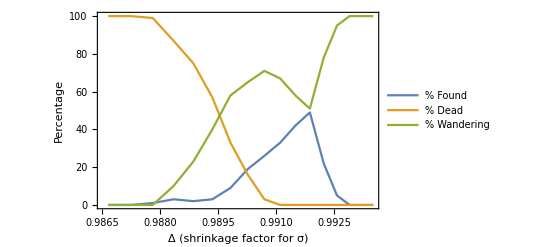

```mathematica
ClearAll[experiment];
experiment[lld_,rld_,nδld_,maxRol_,dim_,tol_,maxIter_,theEchoer_]:=
With[{data=Block[{echo=theEchoer},
sweep[lld,rld,nδld,maxRol,getTarget@dim,tol,maxIter]]},
With[{Δs=#["Δ"]&/@data},
ListLinePlot[{{Δs,pctFound/@data}ᵀ,{Δs,pctDead/@data}ᵀ,{Δs,pctWandering/@data}ᵀ},
Frame->True,
FrameLabel->{{"Percentage",""},
{"Δ (shrinkage factor for σ)",
"Seeker versus Δ, dim = "<>ToString[dim]<>", # rollouts = "<>ToString[maxRol]<>"\ntolerance = "<>ToString[tol]<>", # iters/rollout = "<>ToString[maxIter]}},
PlotLegends->{"% Found","% Dead","% Wandering"}]]];
experiment[1.875,2.1875,16,100,20,0.01,1000,Identity]
```

```mathematica
(*experiment[ldFromΔ@0.99985,ldFromΔ@0.99995,16,100,2000,0.01,80000,Identity]*)
```

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/12.0/Executables/wolfram -subkernel -noinit -nopaclet -wstp,6433,16].

Kernels::rdead: Subkernel connected through KernelObject[6,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {24} assigned to KernelObject[6,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[6,local,<defunct>] resurrected as KernelObject[7,local].

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/12.0/Executables/wolfram -subkernel -noinit -nopaclet -wstp,6432,15].

Kernels::rdead: Subkernel connected through KernelObject[5,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {25} assigned to KernelObject[5,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[5,local,<defunct>] resurrected as KernelObject[8,local].

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/12.0/Executables/wolfram -subkernel -noinit -nopaclet -wstp,6429,12].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[2,local] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {30} assigned to KernelObject[2,local,<defunct>].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[2,local,<defunct>] resurrected as KernelObject[9,local].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

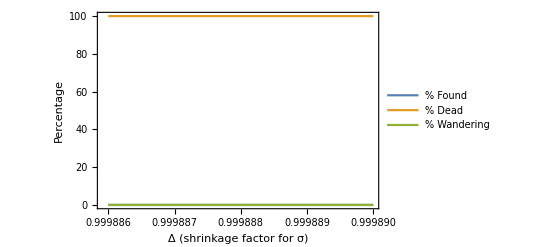

```mathematica
experiment[ldFromΔ@0.999890,ldFromΔ@0.999900,16,100,2000,0.01,160000,Identity]
```

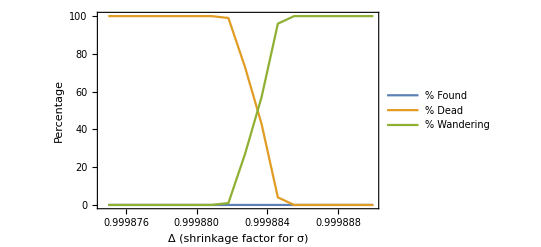

```mathematica
(*experiment[ldFromΔ@0.999875,ldFromΔ@0.99989,16,100,2000,0.01,80000,Identity]*)
```

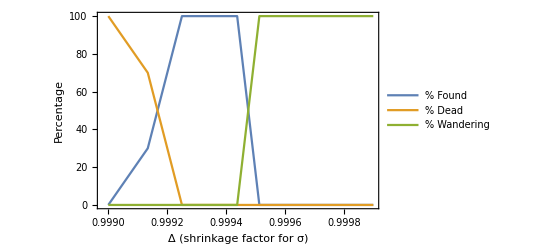

```mathematica
(*experiment[ldFromΔ@0.999,ldFromΔ@0.9999,16,100,200,0.01,20000,Identity]*)
```

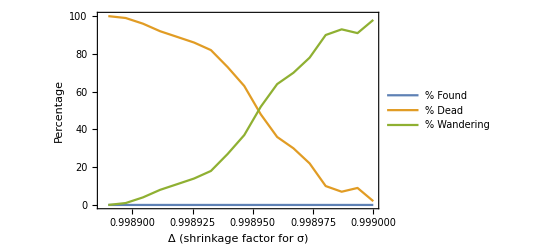

```mathematica
(*experiment[ldFromΔ@0.99889,ldFromΔ@0.999,16,100,200,0.01,10000,Identity]*)
```

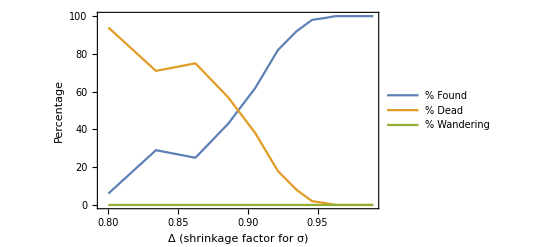

```mathematica
experiment[ldFromΔ@0.80,ldFromΔ@0.99,16,100,2,0.01,1000,Identity]
```

## Junkyard

```mathematica
With[{d=16,l=30/16,r=35/16},ParallelMap[Identity,Range[l,r,(r-l)/d]]]
```

{15/8,485/256,245/128,495/256,125/64,505/256,255/128,515/256,65/32,525/256,265/128,535/256,135/64,545/256,275/128,555/256,35/16}

```mathematica
With[{d=16,l=30/16,r=35/16},Table[l+i(r-l)/d,{i,0,d}]]
```

{15/8,485/256,245/128,495/256,125/64,505/256,255/128,515/256,65/32,525/256,265/128,535/256,135/64,545/256,275/128,555/256,35/16}

```mathematica
Manipulate[
NumberForm[{ΔFromLd@l,ΔFromLd@r,
logarithmicMeanΔ[ΔFromLd@l,ΔFromLd@r]},20],
{{l,1},0,7,1,ControlType->Setter},{{r,7},0,7,1},ControlType->Setter]
```

Test tail-recursion.

```mathematica
ClearAll[testf$];
With[{groundTruth=0.75},
testf$[left_,right_]:=
With[{x=RandomReal[{left,right}]},
If[x<groundTruth,testf$[x,right],
If[x>groundTruth,testf$[left,x],
x]]]];
```

```mathematica
Length@Trace@testf$[0.,1.]
```

433